## Lab 10- Gwen Gorman

Play with the animation in Example 9. Find a combination of values of R,b, and L which produces the red curve you really like.

```mathematica
Manipulate[
Module[
{R=3,b=4,L=10,tmp,ymax,redPoint,f,g,theta},(* Make sure L ≥ R + b *)
If[L<R+b,Abort[]];

ymax=(L-(b-R))Sin[π/4];(* estimated value *)
theta=ArcCos[bluePoint[[1]]/Norm[bluePoint]];
If[bluePoint[[2]]<0,theta=2π-theta];(* 3rd or 4th quadrant *)
bluePoint=R{Cos[theta],Sin[theta]}; (* draw it to the circle always *)
tmp=L/Sqrt[R^2+b^2-2b *R*Cos[theta]];
redPoint={b+(tmp-1)(b-R*Cos[theta]),R(1-tmp)Sin[theta]};

Show[{
Plot[{x},{x,-R-0.1,R+L+0.1},PlotRange->{-ymax,ymax},AspectRatio->Automatic,PlotStyle->White,Ticks->None,ImageSize->350],
(* setup proper canvas so that the frame will not change during animation *)

ParametricPlot[{R Cos[θ],R Sin[θ]},{θ,0,2Pi}],
Graphics[{Blue,PointSize[Large],Point[bluePoint]}],
Graphics[{Black,PointSize[Large],Point[{b,0}]}],
Graphics[{Red,PointSize[Large],Point[redPoint]}],
Graphics[{Black,Line[{redPoint,bluePoint}]}],
Graphics[{Black,Text[O,{-0.15,-0.15}]}],
Graphics[{Black,Text[B,{b,-0.2}]}],
ParametricPlot[Module[{},
tmp=L/Sqrt[R^2+b^2-2b *R*Cos[θ]];
{b+(tmp-1)(b-R*Cos[θ]),R(1-tmp)Sin[θ]}],{θ,0,2π},PlotStyle->Red]
}]],{{bluePoint,{1,1}},Locator},Alignment->Center]
```

Find two pairs of parametric equations to parametrize the parabola x=y^2 for -1≤y≤3, using t as the parameter.

Plot two graphs, one for each pair of parametric equations, separately. Use GraphicsRow to display the two graphs side by side. Do they look the same?

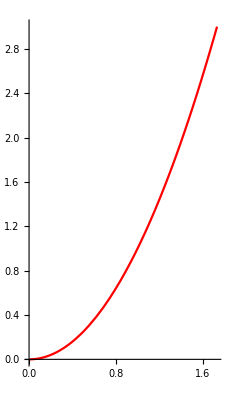

```mathematica
GraphicsRow[{
ParametricPlot[{t,t^2},{t,-1,3},ImageSize->80],
ParametricPlot[{√t,t},{t,-1,3},PlotStyle->Red]
},Spacings->80]
```

the graphs have the same shape

Plot the two parametric curves on one single graph. According to the graph, are the two curves exactly the same?

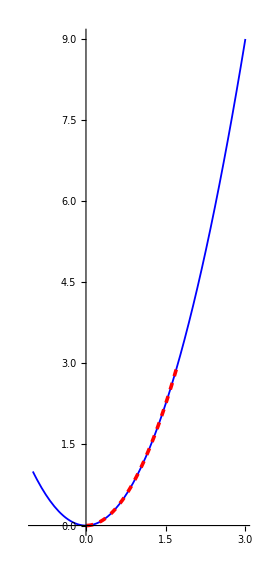

```mathematica
ParametricPlot[{{t,t^2},{√t,t}},{t,-1,3},PlotStyle->{{Thickness[0.005],Blue},{Thickness[0.01],Dashed,Red}},ImageSize->260]
```

Yes the two graphs are the same

Change the code in Example 13 for the ellipse x^2/3^2+y^2/4^2=1.

Plot the ellipse.

{-(12 √2)/(√(25+7 Cos[2 θ])),(12 √2)/(√(25+7 Cos[2 θ]))}

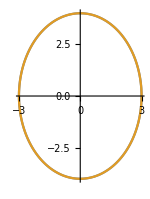

```mathematica
eqn=(x^2)/3^2+(y^2)/4^2==1;
r/.Solve[eqn/.{x->r Cos[θ],y->r Sin[θ]},r]//Simplify
PolarPlot[%,{θ,0,2π},ImageSize->150]
```

Redo 3.1 with % replaced by %[[1]] and %[[2]], separately. What do you obtain?

{-(12 √2)/(√(25+7 Cos[2 θ])),(12 √2)/(√(25+7 Cos[2 θ]))}

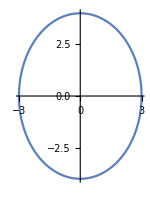

```mathematica
eqn=(x^2)/3^2+(y^2)/4^2==1;
r/.Solve[eqn/.{x->r Cos[θ],y->r Sin[θ]},r]//Simplify
PolarPlot[%[[1]],{θ,0,2π},ImageSize->150]
```

{-(12 √2)/(√(25+7 Cos[2 θ])),(12 √2)/(√(25+7 Cos[2 θ]))}

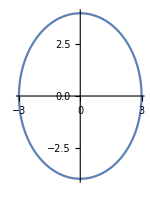

```mathematica
eqn=(x^2)/3^2+(y^2)/4^2==1;
r/.Solve[eqn/.{x->r Cos[θ],y->r Sin[θ]},r]//Simplify
PolarPlot[%[[2]],{θ,0,2π},ImageSize->150]
```

All the graphs seem to be the same except the line changed to blue

Redo 3.2 with 2π replaced by π. What happens?

{-(12 √2)/(√(25+7 Cos[2 θ])),(12 √2)/(√(25+7 Cos[2 θ]))}

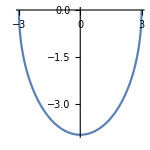

```mathematica
eqn=(x^2)/3^2+(y^2)/4^2==1;
r/.Solve[eqn/.{x->r Cos[θ],y->r Sin[θ]},r]//Simplify
PolarPlot[%[[1]],{θ,0,π},ImageSize->150]
```

Only the bottom half of the ellipse appears on the graph because the domain was changed

Redo 3.1 with 2π replaced by π. Does it still plot an ellipse?

{-(12 √2)/(√(25+7 Cos[2 θ])),(12 √2)/(√(25+7 Cos[2 θ]))}

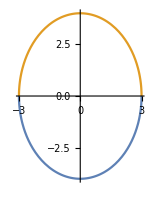

```mathematica
eqn=(x^2)/3^2+(y^2)/4^2==1;
r/.Solve[eqn/.{x->r Cos[θ],y->r Sin[θ]},r]//Simplify
PolarPlot[%,{θ,0,π},ImageSize->150]
```

Yes it still plots an ellipse, however the top half of the ellipse is yellow while the bottom half is blue.

Use ParametricPlot to plot each curve.

y=4 x^2-6x+3,-1≤x≤2

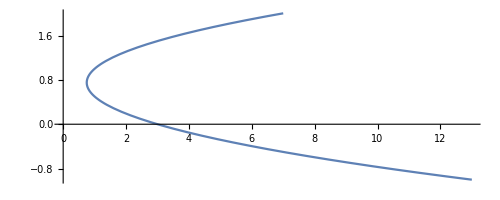

```mathematica
ParametricPlot[{4 t^2-6t+3,t},{t,-1,2}]
```

r=θ sin θ cos^2 θ,0≤θ≤20π

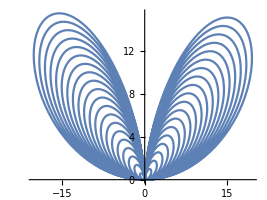

```mathematica
r[t_]:=t*Sin[t]*Cos[t]^2;
ParametricPlot[{r[t]Cos[t],r[t]Sin[t]},{t,0,20Pi}]
```

x=3 t^2-1,y=2t+1,-2≤t≤5

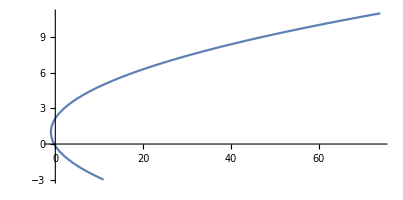

```mathematica
ParametricPlot[{3 t^2-1,2t+1},{t,-2,5}]
```

Refer to Question 4. Use Plot, PolarPlot, and ParametricPlot to plot 4.1, 4.2, and 4.3, respectively. Make sure all curves are merged into one single graph. You had better use first a command like

Plot[{x},{x,-20,20},PlotRange→{-4,15.5},AspectRatio→Automatic,PlotStyle→White]

in Show to set up a proper domain and range for the graph.

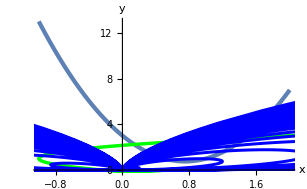

```mathematica
Show[{
Plot[4 x^2-6x+3,{x,-1,2},PlotRange->Automatic,Ticks->None,AxesLabel->{x,y},PlotStyle->Thickness[0.01],ImageSize->200],
ParametricPlot[{3 t^2-1,2t+1},{t,-2,5},PlotStyle->{Green,Thickness[0.008]}],
PolarPlot[t*Sin[t]*Cos[t]^2,{t,0,20π},PlotStyle->{Thickness[0.007],Blue}]}]
```

Use PolarPlot to plot the following polar curves.

The butterfly curve r(θ)=e^(cos θ)-2cos 4θ+sin^3 θ/4,0≤θ≤8π.

```mathematica
PolarPlot[E^Cos[θ]-2Cos[4θ]+Sin[θ/4]^3,{θ,0,8Pi},ImageSize->130]
```

-Graphics-

The butterfly curve r(θ)=e^(sin θ)-2cos 4θ+sin^3 θ/5,0≤θ≤10π.

```mathematica
PolarPlot[E^Sin[θ]-2Cos[4θ]+Sin[θ/5]^3,{θ,0,10Pi},ImageSize->130]
```

-Graphics-

The mosquito curve r(θ)=sin(cos(tan θ)),0≤θ≤2π.

```mathematica
PolarPlot[Sin[Cos[Tan[θ]]],{θ,0,2Pi},ImageSize->130]
```

-Graphics-

Refer to Example 14. Explore the polar curve of r=cos (n θ), where n is an integer. As far as the number of “flower” petals is concerned, what conclusion can you draw about the curve when n is even and when n is odd?

```mathematica
Manipulate[
Show[{
Plot[{x},{x,-1,1},PlotRange->{-1,1},PlotStyle->White,AspectRatio->Automatic,ImageSize->160],

PolarPlot[Cos[n θ],{θ,0,2π}]
}],{{n,4},-20,20,1,Appearance->"Open"},Alignment->Center]
```

When n is an odd number, the flower petals match the value of n. For example, if n=5 then there will be 5 petals. However, when n is even the number of petals is doubled. As seen above, if n=2 then there are 4 petals. If n=4 then there will be 8 petals.

Plot two concentric circles with center the origin and radii 1 and 5. Shade their enclosed region in the second and the fourth quadrants.

```mathematica
Clear["Global`"]
```

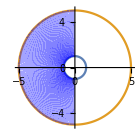

```mathematica
PolarPlotPlus[{r1_,r2_},{θ_,θ1_,θ2_},{regionθ1_,regionθ2_},rmax_,plotGridQ_]:=
Module[{Δθ=Pi/144},
Show[{
If[plotGridQ,
PolarPlot[{r1,r2},{θ,θ1,θ2},PlotRange->rmax,ImageSize->180,
PolarTicks->Automatic,PolarGridLines->Automatic,
GridLinesStyle->Directive[Thickness[.001],Gray,Opacity[0.4]]],
PolarPlot[{r1,r2},{θ,θ1,θ2},PlotRange->rmax,ImageSize->140,PolarTicks->Automatic]],

Table[
Graphics[{Opacity[0.2],Blue,
Module[{f,g,point},
f[t_]=r1/.θ->t; g[t_]=r2/.θ->t;
point[f_,x_]:={f[x]Cos[x],f[x]Sin[x]};
Polygon[{point[f,t],point[f,t+Δθ],point[g,t+Δθ],point[g,t]}]]
}],{t,regionθ1,regionθ2-Δθ,Δθ}]
}]
]
PolarPlotPlus[{1,5},{θ,0,2Pi},{Pi/2,3Pi/2},5.1,False]
```